Άσκηση 2Β_2

```mathematica
ClearAll["Global`*"]
```

(Α)

Τεχνητός δορυφόρος βρίσκεται σε τροχιά και σε κάποια χρονική στιγμή είναι σε ύψος 500km πάνω από τη Γη και έχει ταχύτητα 8km/s παράλληλα προς την επιφάνεια της Γης.

Να βρεθεί:

Η εκκεντρότητα της τροχιάς και ο μεγάλος της ημιάξονας.

Εισάγουμε τις σταθερές που χρειάζονται στο πρόβλημα και τις αρχικές συνθήκες.

```mathematica
G=6.67 10^-11 (*  m^3 kg^1 s^2  *);
M=5.9721986 10^24 (* kg *);
μ=G M;
Rgis=6.3674447 10^6(* m *);
r0={Rgis+5 10^5,0,0};
u0={0,8000,0};
```

Η εκκεντρότητα και ο μεγάλος ημιάξονας βρίσκονται από τις: a=-μ/(2C), e=√(1+(2 C h^2)/μ^2).

```mathematica
(* ενέργεια *) c=1/2 Norm[u0]^2-μ/Norm[r0];
(* στροφορμή *) h=Norm@Cross[r0,u0];
(* εκκεντρότητα *) a=-μ/(2c);
(* μεγάλος ημιάξονας *) e=√(1+(2c h^2)/μ^2);
Column[{
Row[{"C = ",c," J/kg"}],
Row[{"h = ",h," kg m^2/s"}],
Row[{"a = ",a," m"}],
Row[{"e = ",e}]
},
Alignment->Center,
Spacings->1
]
```

C = -2.60049×10^7 J/kg
h = 5.49396×10^10 kg m^2/s
a = 7.65904×10^6 m
e = 0.103354

Το μέγιστο και το ελάχιστο ύψος του δορυφόρου.

Το μέγιστο και το ελάχιστο ύψος θα βρεθούν από το απόγειο και το περίγειο της τροχιάς.

```mathematica
rmin=a(1-e);
rmax=a(1+e);
Column[{
Row[{"h_min = ",rmin-Rgis," m"}],
Row[{"h_max = ",rmax-Rgis," m"}]
}]
```

h_min = 500000. m
h_max = 2.08319×10^6 m

Η περίοδος της κίνησης του.

Η περίοδος της τροχιάς υπολογίζεται από τον τύπο T^2=(4 π^2)/μ a^3.

```mathematica
T=√(4 π^2 a^3/μ);
Row[{"T = ",T/3600," h"}]
```

T = 1.85357 h

(Β)

Τη στιγμή που περνάει από το μέγιστο ύψος, πόσο πρέπει να αυξήσουμε την ταχύτητά του ώστε να μπει σε κυκλική τροχιά;

Η ταχύτητα της τροχιάς υπολογίζεται από την σχέση u^2=μ(2/r-1/a). Για την κυκλική τροχιά ισχύει a=r_max, επομένως η ταχύτητα της κυκλικής τροχιάς είναι u^2=(2μ)/r.

```mathematica
(* ταχύτητα στο rmax της ελλειπτικής τροχιάς *) u1=√(μ(2/rmax-1/a));
(* ταχύτητα της κυκλικής τροχιάς *) u2=√(μ(1/rmax));
Row[{"Δu = ",u2-u1," m/s"}]
```

Δu = 364.475 m/s

Με δεδομένη την παραπάνω κυκλική τροχιά, βρείτε τα Δu_1 και Δu_2 για μια τροχιά μεταφοράς Hohmann ώστε να θέσουμε το δορυφόρο σε γεωστατική τροχιά (T=24h).

Υπολογίζουμε τον μεγάλο ημιάξονα της τροχιάς της μετάβασης.

```mathematica
TGeo=24 3600;
aHoh1=((μ TGeo^2)/(4 π^2))^(1/3);
```

Από αυτόν υπολογίζουμε την ακτίνα της γεωστατικής τροχιάς.

```mathematica
rGeo=2aHoh1-rmax;
```

Οι μεταβολές ταχύτητας τώρα υπολογίζονται από τις Δu_1=√(μ/r_1)(√((2 r_2)/(r_1+r_2))-1), Δu_2=√(μ/r_2)(1-√((2 r_1)/(r_1+r_2))).

```mathematica
Du1=√(μ/rmax)(√((2rGeo)/(rmax+rGeo))-1);
Du2=√(μ/rGeo)(1-√((2rmax)/(rmax+rGeo)));
Column[{
Row[{"Δu_1 = ",Du1," m/s"}],
Row[{"Δu_2 = ",Du2," m/s"}]
},
Alignment->Center,
Spacings->1
]
```

Δu_1 = 2345.35 m/s
Δu_2 = 1265.19 m/s

Πόσο χρόνο διήρκησε η παραπάνω μεταφορά;

```mathematica
Thoh1=√((4 π^2 aHoh1^3)/μ);
Row[{"Χρόνος μετάβασης: ",Thoh1/(2 3600)," h"}]
```

Χρόνος μετάβασης: 12. h

(Γ)

Από την γεωστατική τροχιά βρείτε την Δu_1 ώστε με τροχιά μεταφοράς Hohmann να φτάσει ο δορυφόρος (σκάφος) στη σελήνη.

```mathematica
rLunar=2.413 10^9(* m *);
TLunar=27.322 24 3600 (* s *);
aHoh2=((μ TLunar^2)/(4 π^2))^(1/3);
Du1Lunar=√(μ/rGeo)(√((2rLunar)/(rGeo+rLunar))-1);
Du2Lunar=√(μ/rLunar)(1-√((2rGeo)/(rLunar+rGeo)));
Column[{
Row[{"Δu_1 = ",Du1Lunar," m/s"}],
Row[{"Δu_2 = ",Du2Lunar," m/s"}]
},
Alignment->Center,
Spacings->1
]
```

Δu_1 = 898.401 m/s
Δu_2 = 305.889 m/s

Δώστε σε ένα απόλυτο σύστημα αναφοράς της επιλογής σας τη θέση και την ταχύτητα του σκάφους και τη θέση και την ταχύτητα της σελήνης για να επιτευχθεί η παραπάνω μετάβαση.

```mathematica
Thoh2=√((4 π^2 aHoh2^3)/μ);
Row[{"Χρόνος μετάβασης: ",Thoh2/(2 3600 24)," days"}]
```

Χρόνος μετάβασης: 13.661 days

Θεωρούμε ότι ο δορυφόρος θα ξεκινήσει την μετάβαση από το σημείο (rGeo,0).
Το φεγγάρι θα πρέπει να βρίσκεται την στιγμή που ξεκινάει η μετάβαση του δορυφόρου σε σημείο της τροχιάς του που να απέχει χρόνο ίδιο με αυτόν της μετάβασης.
Θεωρούμε ότι το φεγγάρι κινείται σε κύκλο με σταθερή ταχύτητα.

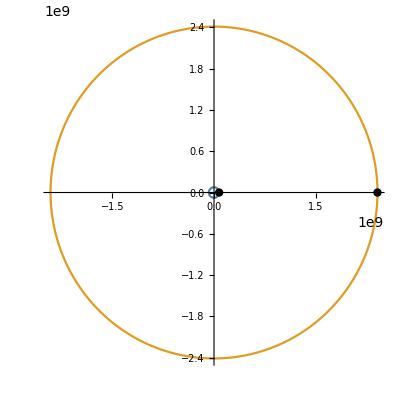

```mathematica
th=2π Thoh2/TLunar;
xL=rLunar Cos[th];
yL=rLunar Sin[th];
Quiet@PolarPlot[{rGeo,rLunar},{th,0,2π},
Epilog->{PointSize[0.015],Point[{{rGeo,0},{xL,yL}}]}
]
```